## 泊松括号、角动量、对称性

## 泊松括号

### 练习2

```mathematica
PoissonBracket[f_,g_,q_List,p_List]/;Length[q]==Length[p]:=Fold[Plus,0,MapThread[D[f,#1] D[g,#2]-D[f,#2] D[g,#1]&,{q,p}]]
(*https://mathematica.stackexchange.com/questions/41850/how-to-define-the-poisson-bracket-in-mathematica*)
```

```mathematica
PoissonBracket[#,1/(2m)p^2+V[q],{q},{p}]&/@{q,p}
```

{p/m,-V'[q]}

## 角动量

### 练习3

```mathematica
PoissonBracket[#[[1]],#[[2]],{x,y,z},{px,py,pz}]&/@{{x,x py-y px},{y,x py-y px},{z,x py-y px}}
```

{-y,x,0}

我们可以得到一个并不意外的结论——对守恒量求泊松括号，将得到一种（具有守恒定律相关对称性的）坐标变换的效果。这是一般性的结论，并且为我们提供了一种思考对称性和守恒性之间关系的思路。

使用Levi-Civita记号，

```mathematica
(*j=3时，等式右边*)
Sum[LeviCivitaTensor[3][[#,3(*固定Lz*),k]]{x,y,z}[[k]],{k,1,3}]&/@Range[3]
```

{-y,x,0}

## 转子与进动

```mathematica
(*等式左边*)
PoissonBracket[#[[1]],#[[2]],{x,y,z},{px,py,pz}]&/@Subsets[{y pz-z py,z px-x pz,x py-y px},{2}]
```

{py x-px y,pz x-px z,pz y-py z}

```mathematica
(*等式右边*)
Sum[LeviCivitaTensor[3][[#[[1]],#[[2]],k]]{y pz-z py,z px-x pz,x py-y px}[[k]],{k,1,3}]&/@Subsets[{1,2,3},{2}]
```

{py x-px y,pz x-px z,pz y-py z}

## 电力与磁力

## 磁场

### 练习3

```mathematica
(*不同矢势定义相同均匀磁场*)
Curl[#,{x,y,z}]&/@{{0,b x,0},{-b y,0,0}}
```

{{0,0,b},{0,0,b}}

```mathematica
(*求解矢势相差梯度的对应标量函数*)
DSolve[Grad[f[x,y,z],{x,y,z}]=={b y,b x,0},f[x,y,z],{x,y,z}]
```

{{f[x,y,z]→b x y+C[1]}}

## 匀强磁场中的运动

### 练习5

使用两种矢势分别求出 
且速度大小恒定，速度z分量守恒
上式两边对时间积分，整理为 
轨道半径为

## 有心力与行星轨道

## 运动方程

```mathematica
<<VariationalMethods`
```

```mathematica
(m/2  (D[r[t]  Cos[θ[t]],t]^2+D[r[t]  Sin[θ[t]],t]^2)+G  M  m/r[t])//EulerEquations[#,{r[t],θ[t]},t]&
```

{m (-(G M)/r[t]^2+r[t] θ'[t]^2-r''[t])==0,-m r[t] (2 r'[t] θ'[t]+r[t] θ''[t])==0}

## 有效势能曲线

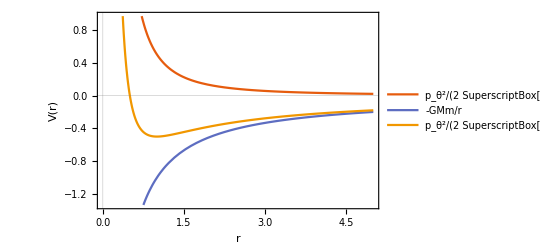

```mathematica
Plot[{1/(2r^2),-1/r,1/(2r^2)-1/r},{r,0,5},PlotTheme->"Scientific",FrameLabel->{"r","V(r)"},PlotLegends->{"p_θ^2/(2 SuperscriptBox[mr, 2])","-GMm/r","p_θ^2/(2 SuperscriptBox[mr, 2])-GMm/r"}]
```

```mathematica
Solve[D[Subscript[p, θ]^2/(2m r^2)-(G M m)/r,r]==0,r]
```

{{r→p_θ^2/(G m^2 M)}}